[1/2] 2-Qubit Mock Data 생성 완료. 스펙트럼 플롯을 출력합니다...

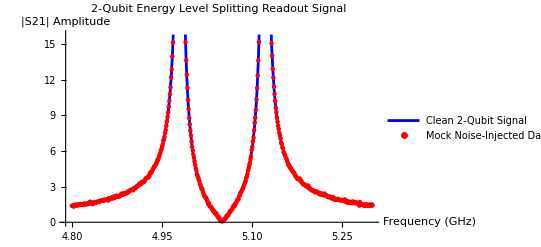

Inverse::luc: Result for Inverse of badly conditioned matrix {«1»} may contain significant numerical errors.

==================================================

[2-Qubit 4D 피셔 행렬 정밀 분석 리포트]

==================================================

• Target SNR          : 100.

• w1 참값 & 오차(CRLB) : 5. GHz  ± 337071. kHz

• w2 참값 & 오차      : 5.1 GHz  ± 337071. kHz

• g12 결합 세기 오차  : 0.05 GHz  ± 337071. kHz

• T2* 디페이징 오차   : 10000. us  ± 141.415 us

--------------------------------------------------

• 4D Parameter Correlation Matrix (상관계수 행렬):

(-1. | 1. | -1. | 1.351×10^-12
1. | -1. | 1. | -1.351×10^-12
-1. | 1. | -1. | 1.351×10^-12
1.351×10^-12 | -1.351×10^-12 | 1.351×10^-12 | 1.)

==================================================

```mathematica
(* =========================================================*)(*STEP 1. 2-큐빗 참값 주입 및 가짜 실측 데이터 (Mock Data) 생성*)(* =========================================================*)ClearAll["Global`*"]

(*1.1 2-큐빗 로렌츠 파형 모델& PSD 모델 (GHz/us 단위 스케일링)*)
(*f,w1,w2,g12->[GHz],T2star->[us]*)
(*T2star 대신 감쇠율 gamma2=1/T2star (GHz 단위)로 변수 치환*)(*T2star=10 us=10,000 ns->gamma2=1/10000=0.0001 GHz*)(*1.1 2-큐빗 로렌츠 파형 모델& PSD 모델 (GHz/us 단위 스케일링)*)(*f,w1,w2,g12->[GHz],T2star->[us]*)tildeS21[f_,w1_,w2_,g12_,T2star_]:=Module[{wPlus,wMinus},wPlus=0.5 (w1+w2+Sqrt[(w1-w2)^2+4 g12^2]);
wMinus=0.5 (w1+w2-Sqrt[(w1-w2)^2+4 g12^2]);
(1/(1/T2star+I 2 Pi (f-wPlus)))+(1/(1/T2star+I 2 Pi (f-wMinus)))];

QubitPSD[f_]:=1.0*^-7+(1.0*^-4/Max[f,0.1]); (*GHz 정규화 PSD*)

(*1.2 참값 주입*)
trueW1=5.0;       (*GHz*)
trueW2=5.1;       (*GHz*)
trueG12=0.05;     (*GHz=50 MHz*)
trueT2star=10000.0;  (*us=10 microseconds*)

(*1.3 VNA 스위프 측정 및 복소 노이즈 주입*)
fData=Range[4.8,5.3,0.001]; (*501 포인트*)
SeedRandom[1234];
noiseLevel=0.05;

realNoise=RandomVariate[NormalDistribution[0,noiseLevel],Length[fData]];
imagNoise=RandomVariate[NormalDistribution[0,noiseLevel],Length[fData]];
complexNoise=realNoise+I*imagNoise;

(*2-큐빗 가짜 실측 데이터*)
mockData=Table[tildeS21[fData[[i]],trueW1,trueW2,trueG12,trueT2star],{i,Length[fData]}]+complexNoise;

(*1.4 시각화*)
dataAbs=Abs[mockData];
trueAbs=Table[Abs[tildeS21[f,trueW1,trueW2,trueG12,trueT2star]],{f,fData}];

Print["[1/2] 2-Qubit Mock Data 생성 완료. 스펙트럼 플롯을 출력합니다..."];
Print[ListPlot[{Thread[{fData,trueAbs}],Thread[{fData,dataAbs}]},PlotStyle->{{Thick,Blue},{Directive[PointSize[0.008],Red]}},Joined->{True,False},PlotLabel->"2-Qubit Energy Level Splitting Readout Signal",AxesLabel->{"Frequency (GHz)","|S21| Amplitude"},PlotLegends->{"Clean 2-Qubit Signal","Mock Noise-Injected Data"}]];

(* =========================================================*)
(*STEP 2. 수치 안정화 2-큐빗 내적 및 피셔 행렬 연산 엔진*)
(* =========================================================*)
QubitFreqIP[a_,b_,PSD_,fmin_,fmax_]:=Chop[Re[4 NIntegrate[(a Conjugate[b])/PSD[f],{f,fmin,fmax},Method->"GaussKronrodRule",MaxRecursion->30,MinRecursion->10]]];

QubitFreqSNR[h_,PSD_,fmin_,fmax_]:=Sqrt[QubitFreqIP[h,h,PSD,fmin,fmax]];

MultiQubitFisherFixedSNR[derivs_,PSD_,fmin_,fmax_,h_,targetSNR_]:=Module[{scalefac,Nderivs,fishermat,i,j},scalefac=(targetSNR/QubitFreqSNR[h,PSD,fmin,fmax])^2;
Nderivs=Length[derivs];
fishermat=Table[0,{i,1,Nderivs},{j,1,Nderivs}];
For[i=1,i<=Nderivs,i++,For[j=1,j<=i,j++,fishermat[[i,j]]=QubitFreqIP[derivs[[i]],derivs[[j]],PSD,fmin,fmax];]];
For[i=1,i<=Nderivs,i++,For[j=i+1,j<=Nderivs,j++,fishermat[[i,j]]=fishermat[[j,i]];]];
scalefac*fishermat];

(* =========================================================*)
(*STEP 3. 2-큐빗 4D 피셔 정밀 분석 파이프라인 가동*)
(* =========================================================*)
RunMultiQubitPipeline[fminIn_,fmaxIn_,w1In_,w2In_,g12In_,T2In_,targetSNR_]:=Module[{w1,w2,g12,T2,h,h1,h2,h3,h4,derivs,GammaMat,CovMat,errs,corrMat},h=tildeS21[f,w1In,w2In,g12In,T2In];
(*4개 변수에 대한 편mi분*)h1=D[tildeS21[f,w1,w2In,g12In,T2In],w1]/. w1->w1In;
h2=D[tildeS21[f,w1In,w2,g12In,T2In],w2]/. w2->w2In;
h3=D[tildeS21[f,w1In,w2In,g12,T2In],g12]/. g12->g12In;
h4=D[tildeS21[f,w1In,w2In,g12In,T2],T2]/. T2->T2In;
derivs={h1,h2,h3,h4};
GammaMat=MultiQubitFisherFixedSNR[derivs,QubitPSD,fminIn,fmaxIn,h,targetSNR];
CovMat=Inverse[GammaMat];
errs=Table[Sqrt[Abs[CovMat[[i,i]]]],{i,1,Length[CovMat]}];
corrMat=Table[CovMat[[i,j]]/Sqrt[Abs[CovMat[[i,i]]*CovMat[[j,j]]]],{i,1,4},{j,1,4}];
Print["\n=================================================="];
Print["   [2-Qubit 4D 피셔 행렬 정밀 분석 리포트]"];
Print["=================================================="];
Print["• Target SNR          : ",targetSNR];
Print["• w1 참값 & 오차(CRLB) : ",w1In," GHz  ± ",errs[[1]]*10^6," kHz"];
Print["• w2 참값 & 오차      : ",w2In," GHz  ± ",errs[[2]]*10^6," kHz"];
Print["• g12 결합 세기 오차  : ",g12In," GHz  ± ",errs[[3]]*10^6," kHz"];
Print["• T2* 디페이징 오차   : ",T2In," us  ± ",errs[[4]]," us"];
Print["--------------------------------------------------"];
Print["• 4D Parameter Correlation Matrix (상관계수 행렬):"];
Print[MatrixForm[SetPrecision[corrMat,4]]];
Print["=================================================="];];

(*파이프라인 가동*)
RunMultiQubitPipeline[4.8,5.3,trueW1,trueW2,trueG12,trueT2star,100.0];
```